## Eigenvalues DQD

```mathematica
Hamiltoniano1={{Subscript[ϵ, L]+Subscript[ϵ, R]+Subscript[e, Z],0,0,0,I*Subscript[t, F]},{0,Subscript[ϵ, L]+Subscript[ϵ, R],0,0,-Subscript[t, n]},{0,0,Subscript[ϵ, L]+Subscript[ϵ, R],0,Subscript[t, n]},{0,0,0,Subscript[ϵ, L]+Subscript[ϵ, R]-Subscript[e, Z],-I*Subscript[t, F]},{-I*Subscript[t, F],-Subscript[t, n],Subscript[t, n],I *Subscript[t, F],2*Subscript[ϵ, R]+u}};
Hamiltoniano2={{-Subscript[e, Z],Subscript[λ, 1],Subscript[λ, 2]},{Subscript[λ, 1],0,Sqrt[2]*τ},{Subscript[λ, 2],Sqrt[2]*τ,ϵ+u}};
MatrixForm[Hamiltoniano1]
MatrixForm[Hamiltoniano2]
ez=1.17;
param={Subscript[λ, 1]->0,Subscript[λ, 2]->Subscript[t, F],τ->Subscript[t, n],Subscript[t, F]->0.1,Subscript[t, n]->0.25,u-> 3000,Subscript[e, Z]->ez,Subscript[ϵ, L]->-ϵ/2,Subscript[ϵ, R]->ϵ/2,ϵ->ϵvar*Subscript[e, Z]-u};
Hamiltoniano1param=Hamiltoniano1//.param;
Hamiltoniano2param=Hamiltoniano2//.param;
```

(e_Z+ϵ_L+ϵ_R | 0 | 0 | 0 | ⅈ t_F
0 | ϵ_L+ϵ_R | 0 | 0 | -t_n
0 | 0 | ϵ_L+ϵ_R | 0 | t_n
0 | 0 | 0 | -e_Z+ϵ_L+ϵ_R | -ⅈ t_F
-ⅈ t_F | -t_n | t_n | ⅈ t_F | u+2 ϵ_R)

(-e_Z | λ_1 | λ_2
λ_1 | 0 | √2 τ
λ_2 | √2 τ | u+ϵ)

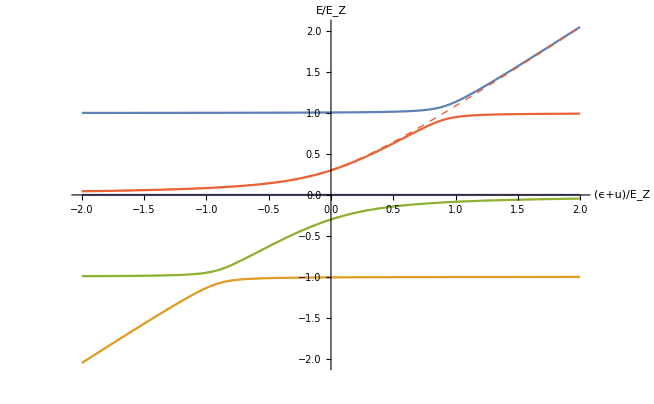

```mathematica
sol1=Eigensystem[Hamiltoniano1param];
energias1=sol1[[1]]/ez;
sol2=Eigensystem[Hamiltoniano2param];
energias2=sol2[[1]]/ez;
Plot[{energias1,energias2},{ϵvar,-2,2},AxesLabel->{"(ϵ+u)/E_Z","E/E_Z"},PlotStyle->{{RGBColor[0.528488, 0.470624, 0.701351]},{RGBColor[0.880722, 0.611041, 0.142051]},{RGBColor[0.560181, 0.691569, 0.194885]},{RGBColor[0.922526, 0.385626, 0.209179]},{RGBColor[0.368417, 0.506779, 0.709798]},{RGBColor[0.880722, 0.611041, 0.142051],Dashed,Thick},{RGBColor[0.560181, 0.691569, 0.194885],Dashed,Thick},{RGBColor[0.922526, 0.385626, 0.209179],Dashed,Thick}}]
```

```mathematica
temp=Simplify[Solve[(Eigenvalues[Hamiltoniano2][[1,1,1]]/. {#1->x,Subscript[λ, 1]->0,Subscript[λ, 2]->0})==0,x]]
```

{{x→1/2 (u+ϵ-√(u^2+2 u ϵ+ϵ^2+8 τ^2))},{x→1/2 (u+ϵ+√(u^2+2 u ϵ+ϵ^2+8 τ^2))},{x→-e_Z}}

## Eigenvalues TQD

```mathematica
H={{e1+EZ/2,0,-tN12,-I*tF12,0,0},{0,e1-EZ/2,-I*tF12,-tN12,0,0},{-tN12,I*tF12,e2+EZ/2,0,-tN23,I*tF23},{I*tF12,-tN12,0,e2-EZ/2,I*tF23,-tN23},{0,0,-tN23,-I*tF23,e3+EZ/2,0},{0,0,-I*tF23,-tN23,0,e3-EZ/2}}
```

{{e1+EZ/2,0,-tN12,-ⅈ tF12,0,0},{0,e1-EZ/2,-ⅈ tF12,-tN12,0,0},{-tN12,ⅈ tF12,e2+EZ/2,0,-tN23,ⅈ tF23},{ⅈ tF12,-tN12,0,e2-EZ/2,ⅈ tF23,-tN23},{0,0,-tN23,-ⅈ tF23,e3+EZ/2,0},{0,0,-ⅈ tF23,-tN23,0,e3-EZ/2}}

```mathematica
MatrixForm[H]
```

(e1+EZ/2 | 0 | -tN12 | -ⅈ tF12 | 0 | 0
0 | e1-EZ/2 | -ⅈ tF12 | -tN12 | 0 | 0
-tN12 | ⅈ tF12 | e2+EZ/2 | 0 | -tN23 | ⅈ tF23
ⅈ tF12 | -tN12 | 0 | e2-EZ/2 | ⅈ tF23 | -tN23
0 | 0 | -tN23 | -ⅈ tF23 | e3+EZ/2 | 0
0 | 0 | -ⅈ tF23 | -tN23 | 0 | e3-EZ/2)

```mathematica
FullSimplify[Eigenvectors[H/.{e1->0,e2->0,e3->0,EZ->0, tF12->tN12*x,tF23->tN23*x}]]
```

{{0,-tN23/tN12,0,0,0,1},{-tN23/tN12,0,0,0,1,0},{0,tN12/tN23,-(ⅈ √(tN12^2+tN23^2) x)/(tN23 √(1+x^2)),(√(tN12^2+tN23^2))/(tN23 √(1+x^2)),0,1},{tN12/tN23,0,(√(tN12^2+tN23^2))/(tN23 √(1+x^2)),-(ⅈ √(tN12^2+tN23^2) x)/(tN23 √(1+x^2)),1,0},{0,tN12/tN23,(ⅈ √(tN12^2+tN23^2) x)/(tN23 √(1+x^2)),-(√(tN12^2+tN23^2))/(tN23 √(1+x^2)),0,1},{tN12/tN23,0,-(√(tN12^2+tN23^2))/(tN23 √(1+x^2)),(ⅈ √(tN12^2+tN23^2) x)/(tN23 √(1+x^2)),1,0}}

## Cambio de base

```mathematica
U=Inverse[{{1,0,0,0,0},{0,1/Sqrt[2],0,1/Sqrt[2],0},{0,1/Sqrt[2],0,-1/Sqrt[2],0},{0,0,1,0,0},{0,0,0,0,1}}];
H=U.Hamiltoniano1.Inverse[U];
MatrixForm[H/.{Subscript[ϵ, L]->-e/2,Subscript[ϵ, R]->e/2}]
Hreducido=H[[3;;5,3;;5]];
MatrixForm[Hreducido/.{Subscript[ϵ, L]->-e/2,Subscript[ϵ, R]->e/2}]
MatrixForm[Hamiltoniano2]
```

(e_Z | 0 | 0 | 0 | ⅈ t_F
0 | 0 | 0 | 0 | 0
0 | 0 | -e_Z | 0 | -ⅈ t_F
0 | 0 | 0 | 0 | -√2 t_n
-ⅈ t_F | 0 | ⅈ t_F | -√2 t_n | e+u)

(-e_Z | 0 | -ⅈ t_F
0 | 0 | -√2 t_n
ⅈ t_F | -√2 t_n | e+u)

(-e_Z | λ_1 | λ_2
λ_1 | 0 | √2 τ
λ_2 | √2 τ | u+ϵ)

```mathematica
FullSimplify[CharacteristicPolynomial[Hreducido/.{Subscript[ϵ, L]->-e/2,Subscript[ϵ, R]->e/2},x]]
```

(e+u-x) x^2+x ((e+u-x) e_Z+t_F^2)+2 (x+e_Z) t_n^2

{{1,0,0,0,0},{0,1/(√2),1/(√2),0,0},{0,0,0,1,0},{0,1/(√2),-1/(√2),0,0},{0,0,0,0,1}}

```mathematica
Eigenvalues[Hreducido//.{Subscript[ϵ, L]->-e/2,Subscript[ϵ, R]->e/2,Subscript[t, F]->0}]
Eigenvalues[Hamiltoniano2//.{Subscript[λ, 1]->0}]
```

{-e_Z,1/2 (e+u-√(e^2+2 e u+u^2+8 t_n^2)),1/2 (e+u+√(e^2+2 e u+u^2+8 t_n^2))}

{Root[#1^3-2 τ^2 e_Z+#1^2 (-u-ϵ+e_Z)+#1 (-2 τ^2-u e_Z-ϵ e_Z-λ_2^2)&,1],Root[#1^3-2 τ^2 e_Z+#1^2 (-u-ϵ+e_Z)+#1 (-2 τ^2-u e_Z-ϵ e_Z-λ_2^2)&,2],Root[#1^3-2 τ^2 e_Z+#1^2 (-u-ϵ+e_Z)+#1 (-2 τ^2-u e_Z-ϵ e_Z-λ_2^2)&,3]}

## Calculo de SOC

```mathematica
Remove["Global`*"]
```

```mathematica
phiL=Sqrt[2/Pi]*Exp[-(x^2+y^2)/l^2 ]/l;
phiR=Sqrt[2/Pi]*Exp[-((x-d)^2+y^2)/l^2 ]/l;
Tminus=(phiL*phiR);
```

```mathematica
Px[f_]:=-I*(D[f,x1]+D[f,x2]);
Py[f_]:=-I*(D[f,y1]+D[f,y2]);
Pplus[f_]:=Px[f]+I*Py[f];
Pminus[f_]:=Px[f]-I*Py[f];
```

```mathematica
norm=Integrate[2*(phiR/.{x->x1,y->y1})+(phiR/.{x->x2,y->y2})*(Pminus[Pminus[Pminus[((phiL/.{x->x1,y->y1})+(phiR/.{x->x2,y->y2})-(phiL/.{x->x2,y->y2})-(phiR/.{x->x1,y->y1}))]]]),{x1,-Infinity,Infinity},{y1,-Infinity,Infinity},{x2,-Infinity,Infinity},{y2,-Infinity,Infinity}]
```

Integrate::idiv: Integral of (2 ⅇ^(-(Times[«2»]+x1)^2/l^2-y1^2/l^2) √(2/π))/l+(16 ⅈ d^3 ⅇ^(-(2 (Times[«2»]+x2)^2)/l^2-(2 y2^2)/l^2))/(l^8 π)-(16 ⅈ d^3 ⅇ^(-(Times[«2»]+x1)^2/l^2-(Times[«2»]+x2)^2/l^2-y1^2/l^2-y2^2/l^2))/(l^8 π)+«36»+(16 ⅇ^(-(2 (Times[«2»]+x2)^2)/l^2-(2 y2^2)/l^2) y2^3)/(l^8 π)-(16 ⅇ^(-x2^2/l^2-(Times[«2»]+x2)^2/l^2-(2 y2^2)/l^2) y2^3)/(l^8 π) does not converge on {-∞,∞}.

∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ((2 ⅇ^((-(-d+x1)^2-y1^2)/l^2) √(2/π))/l+1/l ⅇ^((-(-d+x2)^2-y2^2)/l^2) √(2/π) (-(12 ⅇ^((-x1^2-y1^2)/l^2) √(2/π) y1)/l^5+(12 ⅇ^((-(-d+x1)^2-y1^2)/l^2) √(2/π) y1)/l^5+(8 ⅇ^((-x1^2-y1^2)/l^2) √(2/π) y1^3)/l^7-(8 ⅇ^((-(-d+x1)^2-y1^2)/l^2) √(2/π) y1^3)/l^7-ⅈ ((4 ⅇ^((-x1^2-y1^2)/l^2) √(2/π) x1)/l^5-(4 ⅇ^((-(-d+x1)^2-y1^2)/l^2) √(2/π) (-d+x1))/l^5-(8 ⅇ^((-x1^2-y1^2)/l^2) √(2/π) x1 y1^2)/l^7+(8 ⅇ^((-(-d+x1)^2-y1^2)/l^2) √(2/π) (-d+x1) y1^2)/l^7)+ⅈ (-(4 ⅇ^((-x1^2-y1^2)/l^2) √(2/π) x1)/l^5+(4 ⅇ^((-(-d+x1)^2-y1^2)/l^2) √(2/π) (-d+x1))/l^5+(8 ⅇ^((-x1^2-y1^2)/l^2) √(2/π) x1 y1^2)/l^7-(8 ⅇ^((-(-d+x1)^2-y1^2)/l^2) √(2/π) (-d+x1) y1^2)/l^7-ⅈ ((4 ⅇ^((-x1^2-y1^2)/l^2) √(2/π) y1)/l^5-(4 ⅇ^((-(-d+x1)^2-y1^2)/l^2) √(2/π) y1)/l^5-(8 ⅇ^((-x1^2-y1^2)/l^2) √(2/π) x1^2 y1)/l^7+(8 ⅇ^((-(-d+x1)^2-y1^2)/l^2) √(2/π) (-d+x1)^2 y1)/l^7))+(12 ⅇ^((-x2^2-y2^2)/l^2) √(2/π) y2)/l^5-(12 ⅇ^((-(-d+x2)^2-y2^2)/l^2) √(2/π) y2)/l^5-(8 ⅇ^((-x2^2-y2^2)/l^2) √(2/π) y2^3)/l^7+(8 ⅇ^((-(-d+x2)^2-y2^2)/l^2) √(2/π) y2^3)/l^7-ⅈ (-(4 ⅇ^((-x2^2-y2^2)/l^2) √(2/π) x2)/l^5+(4 ⅇ^((-(-d+x2)^2-y2^2)/l^2) √(2/π) (-d+x2))/l^5+(8 ⅇ^((-x2^2-y2^2)/l^2) √(2/π) x2 y2^2)/l^7-(8 ⅇ^((-(-d+x2)^2-y2^2)/l^2) √(2/π) (-d+x2) y2^2)/l^7)+ⅈ ((4 ⅇ^((-x2^2-y2^2)/l^2) √(2/π) x2)/l^5-(4 ⅇ^((-(-d+x2)^2-y2^2)/l^2) √(2/π) (-d+x2))/l^5-(8 ⅇ^((-x2^2-y2^2)/l^2) √(2/π) x2 y2^2)/l^7+(8 ⅇ^((-(-d+x2)^2-y2^2)/l^2) √(2/π) (-d+x2) y2^2)/l^7-ⅈ (-(4 ⅇ^((-x2^2-y2^2)/l^2) √(2/π) y2)/l^5+(4 ⅇ^((-(-d+x2)^2-y2^2)/l^2) √(2/π) y2)/l^5+(8 ⅇ^((-x2^2-y2^2)/l^2) √(2/π) x2^2 y2)/l^7-(8 ⅇ^((-(-d+x2)^2-y2^2)/l^2) √(2/π) (-d+x2)^2 y2)/l^7))-ⅈ ((4 ⅇ^((-x1^2-y1^2)/l^2) √(2/π) x1)/l^5-(4 ⅇ^((-(-d+x1)^2-y1^2)/l^2) √(2/π) (-d+x1))/l^5-(4 ⅇ^((-x2^2-y2^2)/l^2) √(2/π) x2)/l^5+(4 ⅇ^((-(-d+x2)^2-y2^2)/l^2) √(2/π) (-d+x2))/l^5-(8 ⅇ^((-x1^2-y1^2)/l^2) √(2/π) x1 y1^2)/l^7+(8 ⅇ^((-(-d+x1)^2-y1^2)/l^2) √(2/π) (-d+x1) y1^2)/l^7-ⅈ (-ⅈ ((12 ⅇ^((-x1^2-y1^2)/l^2) √(2/π) x1)/l^5-(8 ⅇ^((-x1^2-y1^2)/l^2) √(2/π) x1^3)/l^7-(12 ⅇ^((-(-d+x1)^2-y1^2)/l^2) √(2/π) (-d+x1))/l^5+(8 ⅇ^((-(-d+x1)^2-y1^2)/l^2) √(2/π) (-d+x1)^3)/l^7)-(4 ⅇ^((-x1^2-y1^2)/l^2) √(2/π) y1)/l^5+(4 ⅇ^((-(-d+x1)^2-y1^2)/l^2) √(2/π) y1)/l^5+(8 ⅇ^((-x1^2-y1^2)/l^2) √(2/π) x1^2 y1)/l^7-(8 ⅇ^((-(-d+x1)^2-y1^2)/l^2) √(2/π) (-d+x1)^2 y1)/l^7)+ⅈ ((4 ⅇ^((-x1^2-y1^2)/l^2) √(2/π) y1)/l^5-(4 ⅇ^((-(-d+x1)^2-y1^2)/l^2) √(2/π) y1)/l^5-(8 ⅇ^((-x1^2-y1^2)/l^2) √(2/π) x1^2 y1)/l^7+(8 ⅇ^((-(-d+x1)^2-y1^2)/l^2) √(2/π) (-d+x1)^2 y1)/l^7)+(8 ⅇ^((-x2^2-y2^2)/l^2) √(2/π) x2 y2^2)/l^7-(8 ⅇ^((-(-d+x2)^2-y2^2)/l^2) √(2/π) (-d+x2) y2^2)/l^7+ⅈ (-(4 ⅇ^((-x2^2-y2^2)/l^2) √(2/π) y2)/l^5+(4 ⅇ^((-(-d+x2)^2-y2^2)/l^2) √(2/π) y2)/l^5+(8 ⅇ^((-x2^2-y2^2)/l^2) √(2/π) x2^2 y2)/l^7-(8 ⅇ^((-(-d+x2)^2-y2^2)/l^2) √(2/π) (-d+x2)^2 y2)/l^7)-ⅈ (-ⅈ (-(12 ⅇ^((-x2^2-y2^2)/l^2) √(2/π) x2)/l^5+(8 ⅇ^((-x2^2-y2^2)/l^2) √(2/π) x2^3)/l^7+(12 ⅇ^((-(-d+x2)^2-y2^2)/l^2) √(2/π) (-d+x2))/l^5-(8 ⅇ^((-(-d+x2)^2-y2^2)/l^2) √(2/π) (-d+x2)^3)/l^7)+(4 ⅇ^((-x2^2-y2^2)/l^2) √(2/π) y2)/l^5-(4 ⅇ^((-(-d+x2)^2-y2^2)/l^2) √(2/π) y2)/l^5-(8 ⅇ^((-x2^2-y2^2)/l^2) √(2/π) x2^2 y2)/l^7+(8 ⅇ^((-(-d+x2)^2-y2^2)/l^2) √(2/π) (-d+x2)^2 y2)/l^7))))ⅆy2ⅆx2ⅆy1ⅆx1

```mathematica
Eigenvectors[{{d,l},{l,-d}}]
```

{{-(-d+√(d^2+l^2))/l,1},{-(-d-√(d^2+l^2))/l,1}}

```mathematica
Solve[Et-(u+e-Sqrt[8t^2+(u+e)^2])/2==d,e]
```

{{e→(-d^2+2 d Et-Et^2+2 t^2-d u+Et u)/(d-Et)}}

```mathematica
sol=Eigensystem[{{Et,0,0},{0,0,Sqrt[2]*tau},{0,Sqrt[2]*tau,e+u}}]
```

{{Et,1/2 (e+u-√(e^2+8 tau^2+2 e u+u^2)),1/2 (e+u+√(e^2+8 tau^2+2 e u+u^2))},{{1,0,0},{0,-(e+u+√(e^2+8 tau^2+2 e u+u^2))/(2 √2 tau),1},{0,(-e-u+√(e^2+8 tau^2+2 e u+u^2))/(2 √2 tau),1}}}

```mathematica
c1unnorm=sol[[2]][[2]][[2]];
c1norm=FullSimplify[c1unnorm/Sqrt[1+c1unnorm^2]]
FullSimplify[Sqrt[1-c1norm^2]]
```

(-e-u-√(8 tau^2+(e+u)^2))/(tau √(16+(2 (e+u) (e+u+√(8 tau^2+(e+u)^2)))/tau^2))

2 √(tau^2/(8 tau^2+(e+u) (e+u+√(8 tau^2+(e+u)^2))))

```mathematica
H={{-ET,l1,l2},{l1,0,tau},{l2,tau,e+u}};
MatrixForm[H]
```

(-ET | l1 | l2
l1 | 0 | tau
l2 | tau | e+u)

```mathematica
Eigensystem[H]
```

{{Root[e l1^2-2 l1 l2 tau-ET tau^2+l1^2 u+(-e ET-l1^2-l2^2-tau^2-ET u) #1+(-e+ET-u) #1^2+#1^3&,1],Root[e l1^2-2 l1 l2 tau-ET tau^2+l1^2 u+(-e ET-l1^2-l2^2-tau^2-ET u) #1+(-e+ET-u) #1^2+#1^3&,2],Root[e l1^2-2 l1 l2 tau-ET tau^2+l1^2 u+(-e ET-l1^2-l2^2-tau^2-ET u) #1+(-e+ET-u) #1^2+#1^3&,3]},{{-tau/l1-(Root[e l1^2-2 l1 l2 tau-ET tau^2+l1^2 u+(-e ET-l1^2-l2^2-tau^2-ET u) #1+(-e+ET-u) #1^2+#1^3&,1] (e l1-l2 tau+l1 u-l1 Root[e l1^2-2 l1 l2 tau-ET tau^2+l1^2 u+(-e ET-l1^2-l2^2-tau^2-ET u) #1+(-e+ET-u) #1^2+#1^3&,1]))/(l1 (l1 tau+l2 Root[e l1^2-2 l1 l2 tau-ET tau^2+l1^2 u+(-e ET-l1^2-l2^2-tau^2-ET u) #1+(-e+ET-u) #1^2+#1^3&,1])),-(e l1-l2 tau+l1 u-l1 Root[e l1^2-2 l1 l2 tau-ET tau^2+l1^2 u+(-e ET-l1^2-l2^2-tau^2-ET u) #1+(-e+ET-u) #1^2+#1^3&,1])/(l1 tau+l2 Root[e l1^2-2 l1 l2 tau-ET tau^2+l1^2 u+(-e ET-l1^2-l2^2-tau^2-ET u) #1+(-e+ET-u) #1^2+#1^3&,1]),1},{-tau/l1-(Root[e l1^2-2 l1 l2 tau-ET tau^2+l1^2 u+(-e ET-l1^2-l2^2-tau^2-ET u) #1+(-e+ET-u) #1^2+#1^3&,2] (e l1-l2 tau+l1 u-l1 Root[e l1^2-2 l1 l2 tau-ET tau^2+l1^2 u+(-e ET-l1^2-l2^2-tau^2-ET u) #1+(-e+ET-u) #1^2+#1^3&,2]))/(l1 (l1 tau+l2 Root[e l1^2-2 l1 l2 tau-ET tau^2+l1^2 u+(-e ET-l1^2-l2^2-tau^2-ET u) #1+(-e+ET-u) #1^2+#1^3&,2])),-(e l1-l2 tau+l1 u-l1 Root[e l1^2-2 l1 l2 tau-ET tau^2+l1^2 u+(-e ET-l1^2-l2^2-tau^2-ET u) #1+(-e+ET-u) #1^2+#1^3&,2])/(l1 tau+l2 Root[e l1^2-2 l1 l2 tau-ET tau^2+l1^2 u+(-e ET-l1^2-l2^2-tau^2-ET u) #1+(-e+ET-u) #1^2+#1^3&,2]),1},{-tau/l1-(Root[e l1^2-2 l1 l2 tau-ET tau^2+l1^2 u+(-e ET-l1^2-l2^2-tau^2-ET u) #1+(-e+ET-u) #1^2+#1^3&,3] (e l1-l2 tau+l1 u-l1 Root[e l1^2-2 l1 l2 tau-ET tau^2+l1^2 u+(-e ET-l1^2-l2^2-tau^2-ET u) #1+(-e+ET-u) #1^2+#1^3&,3]))/(l1 (l1 tau+l2 Root[e l1^2-2 l1 l2 tau-ET tau^2+l1^2 u+(-e ET-l1^2-l2^2-tau^2-ET u) #1+(-e+ET-u) #1^2+#1^3&,3])),-(e l1-l2 tau+l1 u-l1 Root[e l1^2-2 l1 l2 tau-ET tau^2+l1^2 u+(-e ET-l1^2-l2^2-tau^2-ET u) #1+(-e+ET-u) #1^2+#1^3&,3])/(l1 tau+l2 Root[e l1^2-2 l1 l2 tau-ET tau^2+l1^2 u+(-e ET-l1^2-l2^2-tau^2-ET u) #1+(-e+ET-u) #1^2+#1^3&,3]),1}}}

## FAQUAD 2 Levels

```mathematica
Remove["Global`*"]
```

```mathematica
H={{-ET,0,0},{0,0,Sqrt[2]*τ},{0,Sqrt[2]*τ,ϵ+u}};
energies=Eigenvalues[H]
vectors=FullSimplify[Eigenvectors[H],Assumptions->{τ>0,Δ∈Reals}]
```

{-ET,1/2 (u+ϵ-√(u^2+2 u ϵ+ϵ^2+8 τ^2)),1/2 (u+ϵ+√(u^2+2 u ϵ+ϵ^2+8 τ^2))}

{{1,0,0},{0,-(u+ϵ+√((u+ϵ)^2+8 τ^2))/(2 √2 τ),1},{0,(-u-ϵ+√((u+ϵ)^2+8 τ^2))/(2 √2 τ),1}}

```mathematica
FullSimplify[Solve[Δ==-(energies[[2]]+ET)/2,ϵ]][[1]][[1]]
```

ϵ→-ET-u-2 Δ+(2 τ^2)/(ET+2 Δ)

```mathematica
Heff={{Δ,λ},{λ,-Δ}};
energiesEff=Eigenvalues[Heff]
phi=Normalize/@Eigenvectors[Heff]
```

{-√(Δ^2+λ^2),√(Δ^2+λ^2)}

{{-(-Δ+√(Δ^2+λ^2))/(λ √(1+Abs[(-Δ+√(Δ^2+λ^2))/λ]^2)),1/(√(1+Abs[(-Δ+√(Δ^2+λ^2))/λ]^2))},{-(-Δ-√(Δ^2+λ^2))/(λ √(1+Abs[(-Δ-√(Δ^2+λ^2))/λ]^2)),1/(√(1+Abs[(-Δ-√(Δ^2+λ^2))/λ]^2))}}

```mathematica
factor1=FullSimplify[(energiesEff[[1]]-energiesEff[[2]])/Dot[phi[[1]],D[phi[[2]],Δ]],Assumptions->{λ>0,Δ∈ Reals}]
```

(4 (Δ^2+λ^2)^(3/2))/λ

```mathematica
6.582*10^(-1)*Abs[Integrate[1/factor1/.λ->0.1,{Δ,1.7714515969106484,-0.572809903089368}]]
```

3.26387

```mathematica
energiesEff/.{λ->0.1,Δ->-0.572809903089368}
```

{-0.581473,0.581473}

## Short Cut to Adiabaticity TQD

```mathematica
Remove["Global`*"]
```

```mathematica
eq1=dchi==Tan[eta]*(Omega12*Sin[chi]+Omega23*Cos[chi]);
eq2=deta==Omega12*Cos[chi]-Omega23*Sin[chi];
```

```mathematica
FullSimplify[Solve[{eq1,eq2},{Omega12,Omega23}]]
```

{{Omega12→deta Cos[chi]+dchi Cot[eta] Sin[chi],Omega23→dchi Cos[chi] Cot[eta]-deta Sin[chi]}}

```mathematica
chi=Pi*t/(2*tf)-1/3*Sin[2Pi t/tf]+1/24*Sin[4 Pi t/tf];
eta=ArcTan[D[chi,t]/α];
P2=FullSimplify[Sin[eta]^2]
```

(128 π^2 Sin[(π t)/tf]^8)/(35 π^2+72 tf^2 α^2+π^2 (-56 Cos[(2 π t)/tf]+28 Cos[(4 π t)/tf]-8 Cos[(6 π t)/tf]+Cos[(8 π t)/tf]))

```mathematica
FullSimplify[Solve[D[P2,t]==0,t]]
```

{{t→ConditionalExpression[2 tf C[1],C[1]∈ℤ]},{t→ConditionalExpression[1/2 tf (-1+4 C[1]),C[1]∈ℤ]},{t→ConditionalExpression[1/2 tf (1+4 C[1]),C[1]∈ℤ]},{t→ConditionalExpression[tf+2 tf C[1],C[1]∈ℤ]}}

```mathematica
N[P2//. {t->tf/2, tf->20*2Pi/(100*Pi), α->400}]
```

0.00068492

```mathematica
FullSimplify[P2/.t->tf/2]
```

(16 π^2)/(16 π^2+9 tf^2 α^2)

## Tests

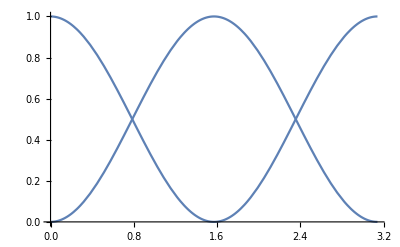

```mathematica
p1=Plot[Cos[x]^2,{x,0,Pi}];
p2=Plot[Sin[x]^2,{x,0,Pi}];
Show[p1,p2]
```

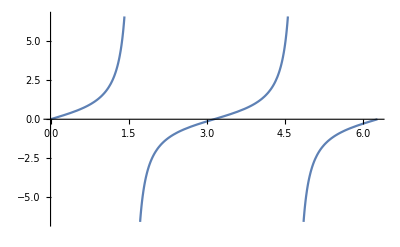

```mathematica
Plot[Tan[x],{x,0,2Pi}]
```

```mathematica
eq1=Sin[χ]*Cos[η]*χ'+η'*Cos[χ]*Sin[η]==Subscript[Ω, 12] Sin[η];
eq2=η'->(Subscript[Ω, 12] Cos[χ]-Subscript[Ω, 23] Sin[χ]);
```

```mathematica
FullSimplify [Solve[eq1/.eq2,χ']]
```

{{χ'→(Sin[χ] Ω_12+Cos[χ] Ω_23) Tan[η]}}